# Special Relativity Diagramming Package

What follows are functions that return graphics objects to feed into Graphics inside of SpacetimeEnvironment.

```mathematica
L[p_,ν_]:=Flatten[1/(√(1-ν^2))({{1, ν}, {ν, 1}}).p];
StaticEvent[label_,{x_,t_},causalityConeQ_]:={Red,If[causalityConeQ,{Line[{{x,t}-{10,10},{x,t}+{10,10}}],Line[{{x,t}-{-10,10},{x,t}+{-10,10}}]}],Black,Point[{x,t}],Text[label,{x,t}+{.1,.2}]}
DynamicEvent[label_,{x_,t_},causalityConeQ_]:=DynamicModule[{xdy=x,tdy=t},{Red,If[causalityConeQ,{Thickness[.008],Line[{Dynamic[{xdy,tdy}-{10,10}],Dynamic[{xdy,tdy}+{10,10}]}],Line[{Dynamic[{xdy,tdy}-{-10,10}],Dynamic[{xdy,tdy}+{-10,10}]}]}],Black,Locator[Dynamic[{xdy,tdy}]],Text[label,Dynamic[{xdy,tdy}+{.1,.2}]]}]
SpacetimeGrid[spacing_]:=Flatten[{Black,Table[Line[{{-10,k},{10,k}}],{k,-2,2,spacing}],Table[Line[{{k,-10},{k,10}}],{k,-2,2,spacing}]}]
CausalityGrid[spacing_]:=Flatten[{Pink,Thickness[.002],Table[Line[{{-6,-6+k},{6,6+k}}],{k,-6,6,spacing}],Table[Line[{{-6,6+k},{6,-6+k}}],{k,-6,6,spacing}]}]
ConstantWorldLine[label_,ν_,p_]:={Thickness[.008],Line[{p-{10,10/ν},p+{10,10/ν}}],Text[label,p+{.15,.25}]}
WorldLine[label_,γ_,p_]:={BSplineCurve[Table[γ[s],{s,0,1,.01}]],Text[label,p+{.15,.25}]}
SimultaneityLine[label_,m_,p_]:={Dashed,Thickness[.006],Line[{p-{10,10m},p+{10,10m}}],Text[label,p+{.15,.25}]}
Hyperbolas[spacing_]:=Flatten[{LightPurple,Thickness[.008],Table[BSplineCurve[Table[r{Cosh[5s],Sinh[5s]},{s,-1,1,.05}]],{r,-2,2,spacing}],Table[BSplineCurve[Table[r{Sinh[5s],Cosh[5s]},{s,-1,1,.05}]],{r,-2,2,spacing}]}]
HistoryTracer[label_,{x_,t_}]:=DynamicModule[{x1=x,t1=t},{Locator[Dynamic[{x1,t1}]],Dynamic[Line[{{x1,t1},{x1,t1}+{10,-10}}]],Dynamic[Line[{{x1,t1},{x1,t1}+{-10,-10}}]],Black,Dynamic[Text[label,{x1+.2,t1+.1}]]}]
FutureTracer[label_,{x_,t_}]:=DynamicModule[{x1=x,t1=t},{Locator[Dynamic[{x1,t1}]],Dynamic[Line[{{x1,t1},{x1,t1}+{10,10}}]],Dynamic[Line[{{x1,t1},{x1,t1}+{-10,10}}]],Black,Dynamic[Text[label,{x1+.2,t1+.1}]]}]
CausalityTracer[label_,{x_,t_}]:=DynamicModule[{x1=x,t1=t},{Locator[Dynamic[{x1,t1}]],Dynamic[Line[{{x1,t1}+{10,-10},{x1,t1}+{-10,10}}]],Dynamic[Line[{{x1,t1}+{-10,-10},{x1,t1}+{10,10}}]],Black,Dynamic[Text[label,{x1+.2,t1+.1}]]}]
ProperlyTickedWorldLine[start_,ν_,ticks_,control_,label_]:={Line[{start,start+control ticks{ν,1}/√(1-ν^2)}],Table[Line[{start+control k{ν,1}/√(1-ν^2)+-.1Normalize[{1,ν}],start+control k{ν,1}/√(1-ν^2)+.1Normalize[{1,ν}]}],{k,1,ticks,1}],Text[label,start+control ticks{ν,1}/√(1-ν^2)+.3Normalize[{ν,1}]]};
ProperlyTickedSimLine[start_,ν_,ticks_,control_,label_]:={Line[{start,start+control ticks{1,ν}/√(1-ν^2)}],Table[Line[{start+control k{1,ν}/√(1-ν^2)-.1Normalize[{ν,1}],start+control k{1,ν}/√(1-ν^2)+.1Normalize[{ν,1}]}],{k,1,ticks,1}],Text[label,start+control ticks{1,ν}/√(1-ν^2)+.3Normalize[{1,ν}]]};
WorldBlock[start_,ν_,properL_,survivalTime_]:=Polygon[Map[(1/(√(1-ν^2))({{1, ν}, {ν, 1}}).(start+#))&,{{0,0},{properL,0},{properL,survivalTime},{0,survivalTime}}]];
CausalDiamond[start_,ν_,properStick_,properTick_]:=Polygon[Map[(1/(√(1-ν^2))({{1, ν}, {ν, 1}}).(start+#))&,{{0,0},{properStick/2,properTick/2},{0,properTick},{-properStick/2,properTick/2}}]];
SynchronizationBox[corner1_,corner2_,ν_,t0_,thic_]:={Blue,Disk[L[corner1,ν],.11],Disk[L[{corner2[[1]],corner1[[2]]},ν],.11],Disk[L[{corner1[[1]],corner2[[2]]},ν],.11],Disk[L[corner2,ν],.11],Thickness->thic,Line[{L[corner1,ν]+{.055,0},L[{corner2[[1]],corner1[[2]]},ν]+{-.055,0}}],Line[{L[{corner1[[1]],corner2[[2]]},ν]+{.055,0},L[corner2,ν]+{-.055,0}}],Line[{L[corner1,ν]+{0,.055},L[{corner1[[1]],corner2[[2]]},ν]+{0,-.055}}],Line[{L[{corner2[[1]],corner1[[2]]},ν]+{0,.055},L[corner2,ν]+{0,-.055}}],White,Disk[L[corner1,ν],.09],Disk[L[{corner2[[1]],corner1[[2]]},ν],.09],Disk[L[{corner1[[1]],corner2[[2]]},ν],.09],Disk[L[corner2,ν],.09],Black,Thickness->.004,Line[{L[corner1,ν],L[corner1,ν]+.075ReIm[ⅇ^(ⅈ(corner1[[2]]+t0))]}],Line[{L[{corner2[[1]],corner1[[2]]},ν],L[{corner2[[1]],corner1[[2]]},ν]+.075ReIm[ⅇ^(ⅈ(L[corner1,ν][[2]]+t0))]}],Line[{L[{corner1[[1]],corner2[[2]]},ν],L[{corner1[[1]],corner2[[2]]},ν]+.075ReIm[ⅇ^(ⅈ(L[corner2,ν][[2]]+t0))]}],Line[{L[corner2,ν],L[corner2,ν]+.075ReIm[ⅇ^(ⅈ(L[corner2,ν][[2]]+t0))]}]};
EinsteinsSynchronization[scale_,ν_,thic_]:=Flatten[Table[SynchronizationBox[{x,y},{x+scale,y+scale},ν,0,thic],{y,-3,3,scale},{x,-3,3,scale}]];
```

SpacetimeEnvironment is the main function of the package. It takes a list of objects to draw.

```mathematica
SpacetimeEnvironment[objects_]:=Show[Plot[{10},{x,-2,2},PlotRange->2.1,AspectRatio-> 1,AxesLabel->{"Space","Time"}],Graphics[Flatten[objects,1]]]
BoostableSpacetimeEnvironment[objects_]:=DynamicModule[{ν=0},Column[{Slider[Dynamic[ν],{-1,1}],Show[Plot[{10},{x,-2,2},PlotRange->2.1,AspectRatio-> 1,AxesLabel->{"Space","Time"}],Graphics[Flatten[objects,1]]]}]]
```

```mathematica
BoostableSpacetimeEnvironment[{}]
```

## Workspace

## Twin Paradox

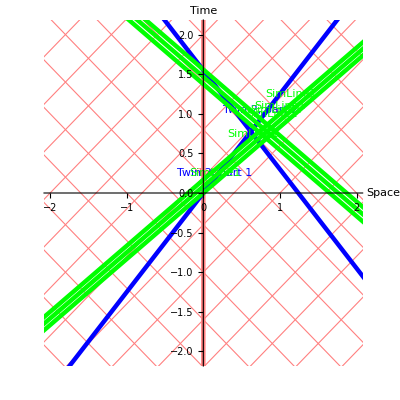

```mathematica
SpacetimeEnvironment[{CausalityGrid[.6],ConstantWorldLine["Twin 1                    ",0.000001,{0,0}],Blue,ConstantWorldLine["\n\n        Twin 2, part 1",.8,{0,0}],ConstantWorldLine["\n\n        Twin 2, part 2",-.8,{.6,.8}],Green,ConstantWorldLine["SimLine1",1.2,{0,0}],ConstantWorldLine["SimLine1",1.2,{.5,.5}],ConstantWorldLine["SimLine1",1.2,{1,1}],ConstantWorldLine["SimLine1",-1.2,{.75,.75}],ConstantWorldLine["SimLine1",-1.2,{.8,.8}],ConstantWorldLine["SimLine1",-1.2,{.85,.85}]}]
```

```mathematica
SpacetimeEnvironment[{CausalityGrid[.7],Hyperbolas[.4],StaticEvent["𝒜",{1.1,1},True],DynamicEvent["ℬ",{-1,1},False],DynamicEvent["𝒞",{-1,.5},False],FontSize->20,ConstantWorldLine["     ♃",.6,{-0.2,.6}],WorldLine["♄  ",{Sin[1.7#],3#-1}&,{.25,-1}],SimultaneityLine["",0,{0,.2}]}]
```

-Graphics-

## Moon Simultaneity Example for Section 2.1 of SR Seminar

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],SimultaneityLine["\nSimultaneity",0,{-.1,1}],FontSize->20,ConstantWorldLine["♁",0.01,{-.5,-.5}],FontSize->12,ConstantWorldLine["☾",0.01,{.5,-.5}],PointSize->.015,StaticEvent["            Landing",{.504,0},False],StaticEvent["                    Planting Flag",{.51,1},False],StaticEvent["Landing                     \n Announcement                                 ",{-.49,1},False],CausalityTracer["",{0,0}]}]
```

-Graphics-

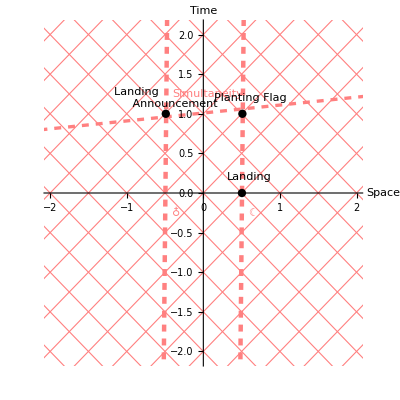

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],SimultaneityLine["\nSimultaneity",.1,{-.1,1}],FontSize->20,ConstantWorldLine["♁",0.01,{-.5,-.5}],FontSize->12,ConstantWorldLine["☾",0.01,{.5,-.5}],PointSize->.015,StaticEvent["            Landing",{.504,0},False],StaticEvent["                    Planting Flag",{.51,1},False],StaticEvent["Landing                     \n Announcement                                 ",{-.49,1},False]}]
```

## Antimatter and Tachyons

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],Green,ConstantWorldLine["Observer                          ",0.0000001,{0,1.2}],Blue,ConstantWorldLine["                                        Tachyon",1.75,{0.5,.5}],Orange,ConstantWorldLine["Normal               \nParticle                    ",.4,{-.2,-2}],Pink,CausalityTracer["P",{0,0}]}]
```

-Graphics-

## Optical Doppler Effect

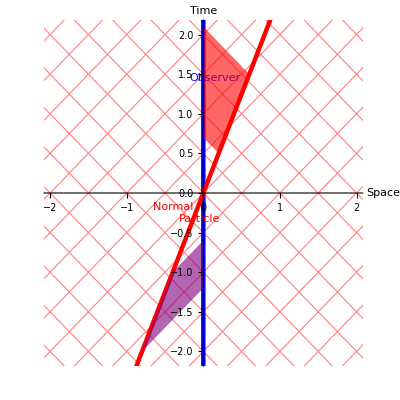

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],Blue,ConstantWorldLine["Observer                          ",0.0000001,{0,1.2}],Red,ConstantWorldLine["Normal               \nParticle                    ",.4,{-.2,-.5}],Opacity[.6],Purple,Polygon[{{-.8,-2},{-.4,-1},{0,-.6},{0,-1.2}}],Red,Polygon[{{.2,.5},{.6,1.5},{0,2.1},{0,.7}}]}]
```

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],Orange,ConstantWorldLine["Observer                          ",0.0000001,{0,1.2}],FontSize->15,Green,Text["e^-",{-.2,.9}],Line[{{0,1},{-1,-4}}],Text["e^+",{.2,.9}],Line[{{0,1},{1,-4}}],HistoryTracer["P",{0,0}]}]
```

-Graphics-

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],Blue,ConstantWorldLine["  Observer                          ",0.0000001,{0,1.5}],Orange,FontSize->15,Text["e^-               ",{-.2,.9}],Line[{{0,-1.5},{-1,4}}],Green,Text["               e^+",{.2,.9}],Line[{{0,-1.5},{1,4}}],Pink,HistoryTracer["P",{0,0}]}]
```

-Graphics-

## Feynman Diagram

```mathematica
Graphics[{Arrow[{{-√2-.7,-√2},{-1,0}}],Arrow[{{-1,0},{1,0}}],Arrow[{{1,0},{.7+√2,-√2}}],BSplineCurve[Table[({{Cos[π/4], Sin[π/4]}, {-Sin[π/4], Cos[π/4]}}).{k,.2Sin[50k]}+{-1,0},{k,-0,-2,-.01}]],BSplineCurve[Table[({{Cos[-π/4], Sin[-π/4]}, {-Sin[-π/4], Cos[-π/4]}}).{k,.2Sin[50k]}+{1,0},{k,0,2,.01}]],FontSize->18,Text["e^-",{-1.6,-.4}],Text["e^+",{1.7,-.4}],Text["γ",{-1.2,.9}],Text["γ",{1.2,.9}]},PlotRange->{{-3,3},{-3,3}}]
```

-Graphics-

## Teleportation

```mathematica
SpacetimeEnvironment[{CausalityGrid[.5],Line[{{},{}}]}]
```

-Graphics-

## Website Photo

```mathematica
SpacetimeEnvironment[{FontSize->13,DynamicEvent["𝒜  ",{.3,.2},True],DynamicEvent["\n\n  ℬ",{.3,.2},False],Blue,ConstantWorldLine["    𝒫_1",.3,{.9,1.2}],StaticEvent["C  ",{-1,-1.1},True]}]
```

-Graphics-

## Spacetime Ruler

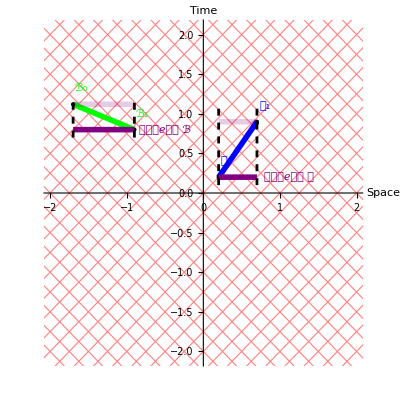

```mathematica
SpacetimeEnvironment[{CausalityGrid[.25],Thickness[.01],Blue,Line[{{.2,.2},{.7,.9}}],FontSize->13,StaticEvent[Style["\n\n\n𝒜_0       ",{FontColor->Blue}],{.2,.2},False],StaticEvent[Style["      𝒜_1      ",{FontColor->Blue}],{.7,.9},False],Green,Line[{{-.9,.8},{-1.7,1.12}}],FontSize->13,StaticEvent[Style["\n\n\nℬ_0           ",{FontColor->Green}],{-1.7,1.12},False],StaticEvent[Style["         ℬ_1      ",{FontColor->Green}],{-.9,.8},False],Purple,Line[{{.2,.2},{.7,.2}}],Text["𝒪𝒷𝒿ℯ𝒸𝓉 𝒜",{1.12,.2}],Line[{{-1.7,.8},{-.9,.8}}],Text["𝒪𝒷𝒿ℯ𝒸𝓉 ℬ",{-.5,.8}],Opacity[.2],Line[{{.2,.9},{.7,.9}}],Line[{{-1.7,1.12},{-.9,1.12}}],Opacity[1],Thickness[.005],Black,Dashed,Line[{{.2,.1},{.2,1.1}}],Line[{{.7,.1},{.7,1.1}}],Line[{{-1.7,.7},{-1.7,1.2}}],Line[{{-.9,.7},{-.9,1.2}}]}]
```

## The One-Electron Universe

```mathematica
Manipulate[SpacetimeEnvironment[{CausalityGrid[.35],Blue,Thickness[.01],Line[points]}],{{points,{{0,0}}},Locator,LocatorAutoCreate->True},Button["Print Points",{Print[points]}]]
```

```mathematica
myPoints=1.3*N[{{2.0833333333333335,1.5950000000000002},{1.5060000000000002,1.0899999999999999},{0.5740000000000003,1.5150000000000001},{-0.5219999999999998,0.9199999999999999},{-1.9859999999999998,2.1},{-0.9579999999999997,2.095},{0.5780000000000003,1.5150000000000001},{0.8540000000000001,0.30500000000000016},{-0.46999999999999975,-0.050000000000000266},{-0.5239999999999998,0.915},{-1.1079999999999999,0.605},{-1.6219999999999999,-0.21999999999999997},{-2.0833333333333335,-1.155},{-1.2659999999999998,-1.695},{-2.0833333333333335,-1.875},{-2.0833333333333335,0.7149999999999999},{-1.1099999999999999,0.605},{-0.46999999999999975,-0.04499999999999993},{-1.6219999999999999,-0.2250000000000001},{-0.7279999999999998,-1.145},{-1.2619999999999998,-1.7000000000000002},{-0.18999999999999972,-1.5950000000000002},{-0.45599999999999974,-2.1},{1.274,-2.065},{1.1620000000000004,-1.0250000000000001},{-0.18999999999999972,-1.605},{-0.20999999999999974,-0.665},{-0.7219999999999998,-1.145},{-0.11399999999999988,-0.20500000000000007},{-0.20999999999999974,-0.665},{0.4580000000000002,-0.6500000000000001},{-0.10799999999999987,-0.19999999999999996},{0.8420000000000001,0.30500000000000016},{1.5060000000000002,1.0950000000000002},{2.0833333333333335,0.20500000000000007},{2.034,-0.605},{1.52,-0.31499999999999995},{0.4560000000000004,-0.6500000000000001},{1.1720000000000002,-1.02},{1.524,-0.31499999999999995},{2.0833333333333335,-1.87}},1];
```

```mathematica
SpacetimeEnvironment[{CausalityGrid[.35],Orange,Thickness[.01],Line[myPoints],Blue,ConstantWorldLine["          Observer",.000000000001,{0,1}],Purple,CausalityTracer["P",{0,0}]}]
```

-Graphics-

## Newtonian Mechanics Visualization

## Simultaneity Graphs

```mathematica
Manipulate[Show[ContourPlot[x^2-t^2,{x,-2,2},{t,-2,2},Contours->30,PlotPoints->50,PlotRange->2,AspectRatio->1],ParametricPlot[s Flatten[1/(√(1-ν^2))({{1, -ν}, {-ν, 1}}).({{1}, {0}})],{s,-10,10}],Graphics[Flatten[{PointSize->.02,Table[{RGBColor[k,0,1-k],Point[Flatten[1/(√(1-ν^2))({{1, -ν}, {-ν, 1}}).({{0}, {k}})]],Point[Flatten[1/(√(1-ν^2))({{1, -ν}, {-ν, 1}}).({{1}, {k}})]]},{k,-2,2,.2}],Yellow,Table[{Line[{{-2+a,-2},{2+a,2}}],Line[{{-2+a,2},{2+a,-2}}]},{a,-4,4,1}]}]]],{{ν,0},-1,1}]
```

```mathematica
SpacetimeEnvironment[{CausalityGrid[.25],Hyperbolas[.25]}]
```

-Graphics-

```mathematica
Manipulate[Show[Plot[{-a Log[Sinh[-x]],-a Log[Sinh[x]]},{x,-2,2},AspectRatio->1,PlotRange->2,PlotPoints->100,PlotStyle->Red],ContourPlot[t^2-x^2==a,{x,-2,2},{t,-2,2},PlotPoints->100]],{{a,1},-3,3}]
```

```mathematica
Clear[x]
D[-Log[Sinh[x]],x]Tanh[x]
```

-1

```mathematica
Manipulate[Show[Plot[{√(a-x^2)Log[x],-√(a-x^2)Log[x]},{x,-2,2},AspectRatio->1,PlotRange->2,PlotPoints->100,PlotStyle->Red],ContourPlot[t^2+x^2==a,{x,-2,2},{t,-2,2},PlotPoints->100]],{{a,1},-3,3}]
```

## Eigenvectors and eigenvalues of Lorentz boosts

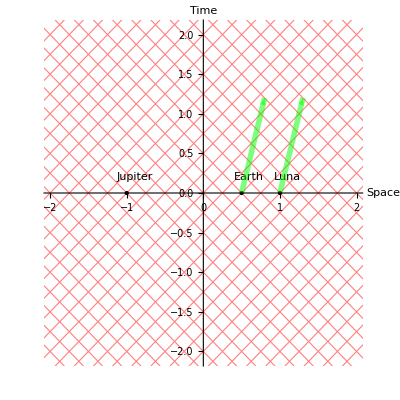

```mathematica
SpacetimeEnvironment[{CausalityGrid[.25],StaticEvent["Jupiter",{-1,0},False],StaticEvent["Earth",{0.5,0},False],StaticEvent["Luna",{1,0},False],Green,Opacity[.5],Thickness[.01],Arrow[{{.5,0},{.5+.3,1.2}}],Arrow[{{1,0},{1+.3,1.2}}]}]
```

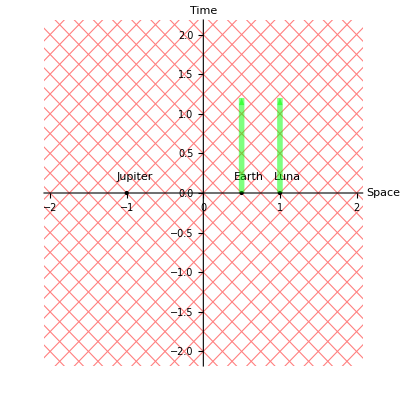

```mathematica
SpacetimeEnvironment[{CausalityGrid[.25],StaticEvent["Jupiter",{-1,0},False],StaticEvent["Earth",{0.5,0},False],StaticEvent["Luna",{1,0},False],Green,Opacity[.5],Thickness[.01],Arrow[{{.5,0},{.5+0,1.2}}],Arrow[{{1,0},{1+0,1.2}}]}]
```

```mathematica
Map[MatrixForm,Eigenvectors[1/(√(1-ν^2))({{1, -ν}, {-ν, 1}})]]
Eigenvalues[1/(√(1-ν^2))({{1, -ν}, {-ν, 1}})]
```

{(1
1),(-1
1)}

{(1-ν)/(√(1-ν^2)),(1+ν)/(√(1-ν^2))}

## Andromeda Paradox

## Teleportation

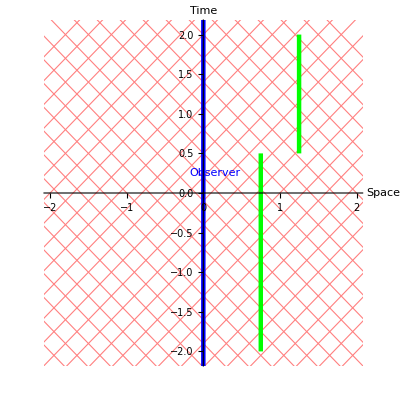

```mathematica
SpacetimeEnvironment[{CausalityGrid[.3],Blue,ConstantWorldLine["Observer                            ",0.0000000001,{0,0}],Green,Line[{{.75,-2},{.75,.5}}],Line[{{1.25,.5},{1.25,2}}]}]
```

```mathematica
Manipulate[Show[Plot[{},{x,-2,2},PlotRange->2,AspectRatio->1,ImageSize->Medium],Graphics[{Thickness[.01],Blue,Opacity[.5],Polygon[{{0,0},{-.5,.5},{0,1},{.5,.5}}],Line[{{0,-2},{0,2}}],Yellow,Polygon[q],Line[{{-1,-2},{1,2}}],CausalityGrid[.25]}]],{{q,{{-1,-1}}},Locator,LocatorAutoCreate->True}]
```

## Length Contraction Diagram - Einstein

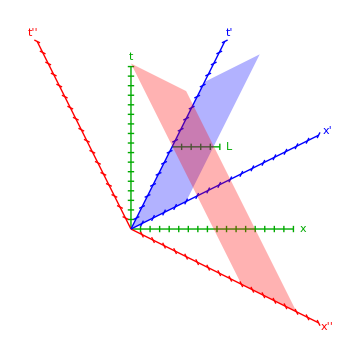

```mathematica
control=.3;ν1=.5;ν2=-.5;ticks=17;properL=5;
Show[Graphics[{FontSize->14,Darker[Green],ProperlyTickedWorldLine[{0,0},.0001,ticks,control,"t"],ProperlyTickedSimLine[{0,0},0.0001,ticks,control,"x"],ProperlyTickedSimLine[2.58{ν1,1},.0001,5,control,"L"],Blue,ProperlyTickedWorldLine[{0,0},ν1,ticks,control,"t'"],ProperlyTickedSimLine[{0,0},ν1,ticks,control,"x'"],Opacity[.3],WorldBlock[{0,0},ν1,control properL,4],Opacity[1],Red,ProperlyTickedWorldLine[{0,0},ν2,ticks,control,"t''"],ProperlyTickedSimLine[{0,0},ν2,ticks,control,"x''"],Opacity[.3],WorldBlock[{3,0},ν2,control properL,6],Opacity[1]},ImageSize->Medium]]
```

## Various Length Contractions Diagram

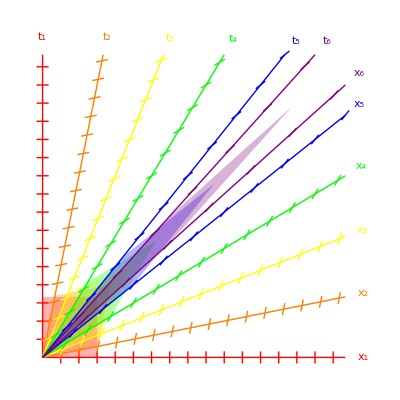

```mathematica
control=.3;ν1=0.00001;ν2=.2;ν3=.4;ν4=.6;ν5=.8;ν6=.9;ticks=5/control;properL=3;survT=1;
Graphics[{Red,ProperlyTickedWorldLine[{0,0},ν1,√(1-ν1^2)ticks,control,"t_1"],ProperlyTickedSimLine[{0,0},ν1,√(1-ν1^2)ticks,control,"x_1"],Opacity[.3],WorldBlock[{0,0},ν1,control properL,survT],Opacity[1],
Orange,ProperlyTickedWorldLine[{0,0},ν2,√(1-ν2^2)ticks,control,"t_2"],ProperlyTickedSimLine[{0,0},ν2,√(1-ν2^2)ticks,control,"x_2"],Opacity[.3],WorldBlock[{0,0},ν2,control properL,survT],Opacity[1],
Yellow,ProperlyTickedWorldLine[{0,0},ν3,√(1-ν3^2)ticks,control,"t_3"],ProperlyTickedSimLine[{0,0},ν3,√(1-ν3^2)ticks,control,"x_3"],Opacity[.3],WorldBlock[{0,0},ν3,control properL,survT],Opacity[1],
Green,ProperlyTickedWorldLine[{0,0},ν4,√(1-ν4^2)ticks,control,"t_4"],ProperlyTickedSimLine[{0,0},ν4,√(1-ν4^2)ticks,control,"x_4"],Opacity[.3],WorldBlock[{0,0},ν4,control properL,survT],Opacity[1],
Blue,ProperlyTickedWorldLine[{0,0},ν5,√(1-ν5^2)ticks,control,"t_5"],ProperlyTickedSimLine[{0,0},ν5,√(1-ν5^2)ticks,control,"x_5"],Opacity[.3],WorldBlock[{0,0},ν5,control properL,survT],Opacity[1],
Purple,ProperlyTickedWorldLine[{0,0},ν6,√(1-ν6^2)ticks,control,"t_6"],ProperlyTickedSimLine[{0,0},ν6,√(1-ν6^2)ticks,control,"x_6"],Opacity[.3],WorldBlock[{0,0},ν6,control properL,survT],Opacity[1]}]
```

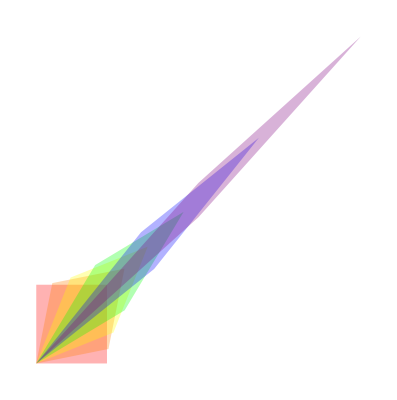

```mathematica
control=.3;ν1=0.00001;ν2=.2;ν3=.4;ν4=.6;ν5=.8;ν6=.9;ticks=5/control;properL=3;survT=1;
Graphics[{Opacity[.3],Red,WorldBlock[{0,0},ν1,control properL,survT],
Orange,WorldBlock[{0,0},ν2,control properL,survT],
Yellow,WorldBlock[{0,0},ν3,control properL,survT],
Green,WorldBlock[{0,0},ν4,control properL,survT],
Blue,WorldBlock[{0,0},ν5,control properL,survT],
Purple,WorldBlock[{0,0},ν6,control properL,survT]}]
```

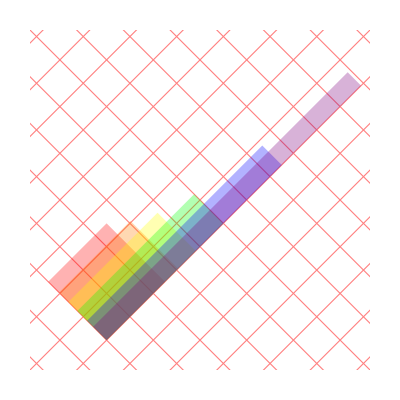

```mathematica
control=1;ν1=0.00001;ν2=.2;ν3=.4;ν4=.6;ν5=.8;ν6=.9;ticks=5/control;properL=1;survT=1;
Show[Plot[{},{x,-3,3},PlotRange->{{-.6,2.2},{-.2,2.6}},AspectRatio->1,Axes->False],Graphics[{CausalityGrid[.4],Opacity[.3],Red,CausalDiamond[{0,0},ν1,control properL,survT],
Orange,CausalDiamond[{0,0},ν2,control properL,survT],
Yellow,CausalDiamond[{0,0},ν3,control properL,survT],
Green,CausalDiamond[{0,0},ν4,control properL,survT],
Blue,CausalDiamond[{0,0},ν5,control properL,survT],
Purple,CausalDiamond[{0,0},ν6,control properL,survT]}]]
```

## Einstein’s Synchronization, Boxes and Diamonds

```mathematica
Manipulate[SpacetimeEnvironment[{Hyperbolas[.2],SynchronizationBox[{0,1.2},{.5,.9},ν,t0]}],{{ν,0},-1,1},{{t0,0},-2π,2π}]
```

```mathematica
Manipulate[SpacetimeEnvironment[{CausalityGrid[.5],EinsteinsSynchronization[.5,ν,.01]}],{{ν,0},-1,1}]
```

## Actually doing the Einstein-Poincaré Synchronization

{{-0.4,-1.4},{0,-1.4},{0,-1},{0.4,-1},{-0.4,-1},{-0.8,-1},{0,-0.6},{0.4,-0.6},{-0.4,-0.6},{-0.8,-0.6},{0.8,-0.6},{-1.2,-0.6},{0,0.6},{0.4,0.6},{-0.4,0.6},{-0.8,0.6},{0.8,0.6},{-1.2,0.6},{1.2,0.6},{-1.6,0.6},{1.6,0.6},{-2,0.6},{0,-0.2},{0.4,-0.2},{-0.4,-0.2},{-0.8,-0.2},{0.8,-0.2},{-1.2,-0.2},{1.2,-0.2},{-1.6,-0.2},{0,0.2},{0.4,0.2},{-0.4,0.2},{-0.8,0.2},{0.8,0.2},{-1.2,0.2},{1.2,0.2},{-1.6,0.2},{1.6,0.2},{-2,0.2},{2,0.2},{0,1},{0.4,1},{-0.4,1},{-0.8,1},{0.8,1},{-1.2,1},{1.2,1},{-1.6,1},{1.6,1},{-2,1},{0,1},{0.4,1},{-0.4,1},{-0.8,1},{0.8,1},{-1.2,1},{1.2,1},{-1.6,1},{1.6,1},{-2,1},{0,1.4},{0.4,1.4},{-0.4,1.4},{-0.8,1.4},{0.8,1.4},{-1.2,1.4},{1.2,1.4},{-1.6,1.4},{1.6,1.4},{-2,1.4},{0,1.8},{0.4,1.8},{-0.4,1.8},{-0.8,1.8},{0.8,1.8},{-1.2,1.8},{1.2,1.8},{-1.6,1.8},{1.6,1.8},{-2,1.8}}

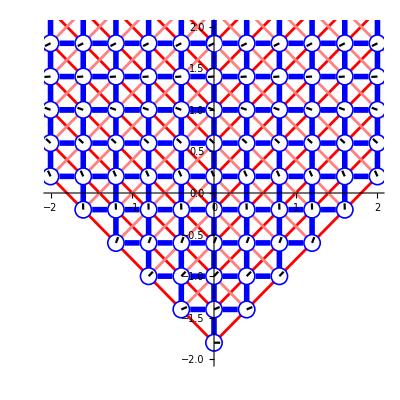

```mathematica
points={{0,-1.8},{0,-1.4},{.4,-1.4},{-.4,-1.4},{0,-1},{.4,-1},{-.4,-1},{-.8,-1},{.8,-1},{0,-.6},{.4,-.6},{-.4,-.6},{-.8,-.6},{.8,-.6},{-1.2,-.6},{1.2,-.6},{0,-.2},{.4,-.2},{-.4,-.2},{-.8,-.2},{.8,-.2},{-1.2,-.2},{1.2,-.2},{-1.6,-.2},{1.6,-.2},{0,.2},{.4,.2},{-.4,.2},{-.8,.2},{.8,.2},{-1.2,.2},{1.2,.2},{-1.6,.2},{1.6,.2},{-2,.2},{2,.2},{0,.6},{.4,.6},{-.4,.6},{-.8,.6},{.8,.6},{-1.2,.6},{1.2,.6},{-1.6,.6},{1.6,.6},{-2,.6},{2,.6},{0,1},{.4,1},{-.4,1},{-.8,1},{.8,1},{-1.2,1},{1.2,1},{-1.6,1},{1.6,1},{-2,1},{2,1},{0,1.4},{.4,1.4},{-.4,1.4},{-.8,1.4},{.8,1.4},{-1.2,1.4},{1.2,1.4},{-1.6,1.4},{1.6,1.4},{-2,1.4},{2,1.4},{0,1.8},{.4,1.8},{-.4,1.8},{-.8,1.8},{.8,1.8},{-1.2,1.8},{1.2,1.8},{-1.6,1.8},{1.6,1.8},{-2,1.8},{2,1.8}};
spac=.4;t0=1.8;
barStarts={{-.4,-1.4},{0,-1.4},{0,-1},{.4,-1},{-.4,-1},{-.8,-1},{0,-.6},{.4,-.6},{-.4,-.6},{-.8,-.6},{.8,-.6},{-1.2,-.6},{0,.6},{.4,.6},{-.4,.6},{-.8,.6},{.8,.6},{-1.2,.6},{1.2,.6},{-1.6,.6},{1.6,.6},{-2,.6},{0,-.2},{.4,-.2},{-.4,-.2},{-.8,-.2},{.8,-.2},{-1.2,-.2},{1.2,-.2},{-1.6,-.2},{0,.2},{.4,.2},{-.4,.2},{-.8,.2},{.8,.2},{-1.2,.2},{1.2,.2},{-1.6,.2},{1.6,.2},{-2,.2},{2,.2},{0,1},{.4,1},{-.4,1},{-.8,1},{.8,1},{-1.2,1},{1.2,1},{-1.6,1},{1.6,1},{-2,1},{0,1},{.4,1},{-.4,1},{-.8,1},{.8,1},{-1.2,1},{1.2,1},{-1.6,1},{1.6,1},{-2,1},{0,1.4},{.4,1.4},{-.4,1.4},{-.8,1.4},{.8,1.4},{-1.2,1.4},{1.2,1.4},{-1.6,1.4},{1.6,1.4},{-2,1.4},{0,1.8},{.4,1.8},{-.4,1.8},{-.8,1.8},{.8,1.8},{-1.2,1.8},{1.2,1.8},{-1.6,1.8},{1.6,1.8},{-2,1.8}}
Show[Plot[{},{x,-2,2},PlotRange->2,AspectRatio->1],Graphics[Flatten[{Thickness[.005],Red,Line[{{0,-1.8},{0,-1.8}+{-2,2}}],Line[{{0,-1.8},{0,-1.8}+{2,2}}],Line[{{0,-1.4},{0,-1.4}+{-2,2}}],Line[{{0,-1.4},{0,-1.4}+{2,2}}],Line[{{0,-1},{0,-1}+{2,2}}],Line[{{0,-1},{0,-1}+{-2,2}}],Line[{{0,-.6},{0,-.6}+{2,2}}],Line[{{0,-.6},{0,-.6}+{-2,2}}],Line[{{0,-.2},{0,-.2}+{2,2}}],Line[{{0,-.2},{0,-.2}+{-2,2}}],Line[{{0,.2},{0,.2}+{2,2}}],Line[{{0,.2},{0,.2}+{-2,2}}],Line[{{0,.6},{0,.6}+{2,2}}],Line[{{0,.6},{0,.6}+{-2,2}}],Line[{{0,1},{0,1}+{2,2}}],Line[{{0,1},{0,1}+{-2,2}}],Line[{{0,1.4},{0,1.4}+{2,2}}],Line[{{0,1.4},{0,1.4}+{-2,2}}],Line[{{0,1.8},{0,1.8}+{2,2}}],Line[{{0,1.8},{0,1.8}+{-2,2}}],Pink,Line[{{-.4,-1.4},{0,-1}}],Line[{{-.4,-1},{0,-.6}}],Line[{{-.8,-1},{0,-.2}}],Line[{{-.8,-.6},{0,.2}}],Line[{{-1.2,-.6},{0,.6}}],Line[{{-1.2,-.2},{0,1}}],Line[{{-1.6,-.2},{0,1.4}}],Line[{{-1.6,.2},{0,1.8}}],Line[{{-2,.2},{0,2.2}}],Line[{{-2,.6},{0,2.6}}],Line[{{-2.4,.6},{0,3}}],Line[{{-2.4,1},{0,3.4}}],Line[{{-2.8,1},{0,3.8}}],Line[{{.4,-1.4},{0,-1}}],Line[{{.4,-1},{0,-.6}}],Line[{{.8,-1},{0,-.2}}],Line[{{.8,-.6},{0,.2}}],Line[{{1.2,-.6},{0,.6}}],Line[{{1.2,-.2},{0,1}}],Line[{{1.6,-.2},{0,1.4}}],Line[{{1.6,.2},{0,1.8}}],Line[{{2,.2},{0,2.2}}],Line[{{2,.6},{0,2.6}}],Line[{{2.4,.6},{0,3}}],Line[{{2.4,1},{0,3.4}}],Line[{{2.8,1},{0,3.8}}],Table[{Blue,Disk[point,.11],Thickness[.01],Line[{point+{0,.055},point+{0,spac}+{0,-.055}}],White,Disk[point,.09],Black,Thickness->.004,Line[{point,point+.075ReIm[ⅇ^(ⅈ (point[[2]]+t0))]}]},{point,points}],Blue,Thickness[.01],Table[Line[{p+{.11,0},p+{spac,0}+{-.11,0}}],{p,barStarts}]}]]]
```

## Theoretical Boost to Infinity

```mathematica
Manipulate[SpacetimeEnvironment[{EinsteinsSynchronization[.37,ν,thic]}],{{ν,0},-1,1},{{thic,.01},0.0001,.01}]
```

```mathematica
108,370
469,442
```